```mathematica
c=2.9979*^8;
ℏ=1.05*^-34;
k=1.3806*^-23;

γ[side_]:=Block[{},
Switch[side,
1,4.521*^13,
2,0,
_,0
]
]
ωp[side_]:=Block[{},
Switch[side,
1,1.37*^16,
2,8.85938*^15,
_,0
]
]
ϵinf[side_]:=Block[{},
Switch[side,
1,1,
2,1.035,
_,0
]
]
ϵ0[side_]:=Block[{},
Switch[side,
1,0,
2,11.87,
_,0
]
]

ϵi[ω_, model_, side_]:=Block[{},
Switch[model,
1,1+(ωp[side]/ω)^2,
2,Switch[side,
1,1+ωp[side]^2/(ω(ω+γ[side])), (* Drude Model *)
2,ϵinf[side]+(ϵ0[side]-ϵinf[side])/(1-(ω/ωp[side])^2) (* Dielectric Model *),
_,0
],
_,0
]
]

r[ω_,κ_,pol_,model_,side_]:=Block[{ϵr,l,r},
ϵr=ϵi[ω,model,side];
l=Sqrt[ω^2*(ϵr-1)+c^2κ];
r=Switch[pol,
1,c κ,
2,c κ*ϵr
];
Return[(l-r)/(l+r)]
]
rsquared[ω_,κ_,pol_,model_]:=r[ω,κ,pol,model,1]*r[ω,κ,pol,model,2]

ωIntegral[κ_,model_,L_]:=Block[{},
integ[lim_?NumberQ]:=NIntegrate[(Log[1-rsquared[ω,κ,1,model]*Exp[-2*κ*L]]+Log[1-rsquared[ω,κ,2,model]*Exp[-2*κ*L]]),{ω,0,lim},AccuracyGoal->3];
integ[c*κ]
]

ηE[model_,L_]:=Block[{},
-((180.0*L^3)/(c*Pi^4))NIntegrate[κ*ωIntegral[κ,model,L],{κ,10.^-1,1.6*^7},AccuracyGoal->3]
]
```

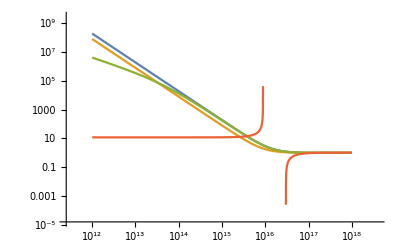

```mathematica
(* Plot Conductivity Models *)
ϵs=Flatten[Table[ϵi[ω,i,j],{i,1,2},{j,1,2}]];
LogLogPlot[ϵs,{ω,10^12,10^18}]
```

```mathematica
ηplasma=Table[{10.0^exp,ηE[1,10.0^(exp)]},{exp,-7,-4,0.1}];
```

```mathematica
ηdrude=Table[{10.0^exp,ηE[2,10.0^(exp)]},{exp,-7,-4,0.1}];
```

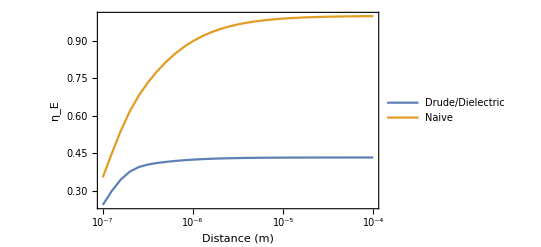

```mathematica
ListLogLinearPlot[{ηdrude,ηplasma},Frame->True,PlotRangePadding->{None,0.1},FrameLabel->{"Distance (m)","η_E"},ImageSize->Scaled[0.8],Joined->True,PlotLegends->{"Drude/Dielectric","Naive"}]
```

```mathematica
Eperfect[L_,R_]:=Block[{},
-(Pi^3ℏ c/720.)(R/(L^2))(1.+0.3333333(L/R))
]

Fperfect[L_,R_]:=Block[{},
(2ℏ c Pi^3/720)*(R/(L^3))*(1+(0.3333333/2.0)*L/R)
]

FPFA[L_,R_]:=Block[{},
(2ℏ c Pi^3/720)*(R/(L^3))
]

ηplasmaInterp=Interpolation[ηplasma];
ηdrudeInterp=Interpolation[ηdrude];
ηInterp[model_,L_]:=Block[{},
Switch[model,
1,ηplasmaInterp[L],
2,ηdrudeInterp[L],
_,0
]
]

ψ[L_,r_,R_]:=R (1-Sqrt[1-r^2/R^2])+L
dψsq[r_,R_]:=1/((R^2/r^2)-1)
Integrand[model_,L_,r_,R_]:=Block[{},
(ηInterp[model,ψ[L,r,R]]/(ψ[L,r,R]^3))(1+(1/3)dψsq[r,R])
]
Integrand0[model_,L_,r_,R_]:=Block[{},
(1/(ψ[L,r,R]^3))(1+(1/3)dψsq[r,R])
]

Ec[model_,L_,R_]:=Block[{},
intval[Lval_?NumericQ]:=NIntegrate[Integrand[model,Lval,r,R],{r,0.0,0.5R},AccuracyGoal->2];
-(2Pi^3 ℏ c/720.)*intval[L]
]

Fc[model_,L_,R_]:=Block[{},
Limit[(Ec[model,L+x,R]-Ec[model,L,R])/x,x->0]
]

f[T_,L_]:=Block[{ξ},
ξ=k*T*L/(ℏ c);
If[ξ≤ 0.5,
(ξ^3/(2Pi))*1.202-(ξ^4Pi^2/45),(ξ/(8Pi))*1.202-(Pi^2/720)
]
]
TempCorrection[T_,L_]:=Block[{},
1.+(720./Pi^2)*f[T,L]
]

FPFAcorrected[model_,L_,R_,T_]:=Block[{},
ηInterp[model,L]*FPFA[L,R]*TempCorrection[T,L]
]

Fcorrected[model_,L_,R_,T_]:=Block[{},
ηInterp[model,L]*Fperfect[L,R]*TempCorrection[T,L]
]
Ecorrected[model_,L_,R_,T_]:=Block[{},
ηInterp[model,L]*Eperfect[L,R]*TempCorrection[T,L]
]
```

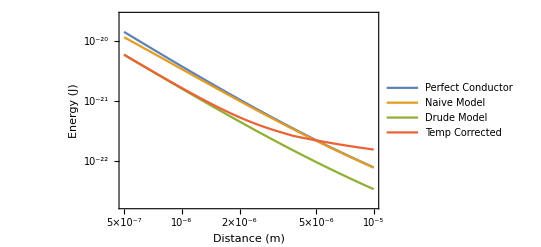

```mathematica
radius=2.5*^-6;
LogLogPlot[{-Eperfect[L,radius],-Ecorrected[1,L,radius,0],-Ecorrected[2,L,radius,0],-Ecorrected[2,L,radius,300]},{L,5.*^-7,1*^-5},Frame->True,PlotRangePadding->{None,0.1},PlotRange->{{5.*^-7,1*^-5},Full},FrameLabel->{"Distance (m)","Energy (J)"},ImageSize->Scaled[0.8],PlotLegends->{"Perfect Conductor","Naive Model","Drude Model","Temp Corrected"}]
```

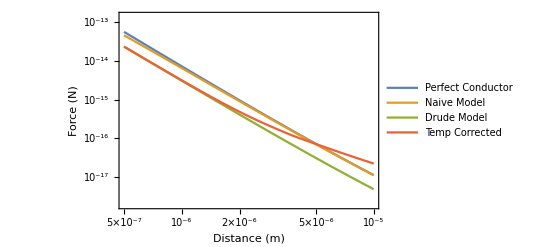

```mathematica
LogLogPlot[{Fperfect[L,radius],Fcorrected[1,L,radius,0],Fcorrected[2,L,radius,0],Fcorrected[2,L,radius,300]},{L,5.0*^-7,1*^-5},Frame->True,PlotRangePadding->{None,0.1},PlotRange->{{5.*^-7,1*^-5},Full},FrameLabel->{"Distance (m)","Force (N)"},ImageSize->Scaled[0.8],PlotLegends->{"Perfect Conductor","Naive Model","Drude Model","Temp Corrected"}]
```

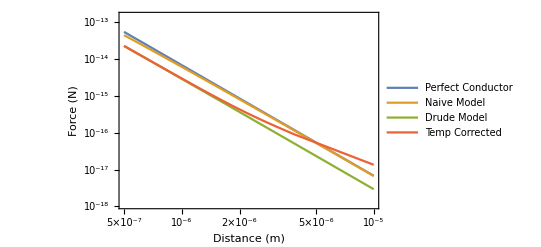

```mathematica
LogLogPlot[{FPFA[L,radius],FPFAcorrected[1,L,radius,0],FPFAcorrected[2,L,radius,0],FPFAcorrected[2,L,radius,300]},{L,5.0*^-7,1*^-5},Frame->True,PlotRangePadding->{None,0.1},PlotRange->{{5.*^-7,1*^-5},Full},FrameLabel->{"Distance (m)","Force (N)"},ImageSize->Scaled[0.8],PlotLegends->{"Perfect Conductor","Naive Model","Drude Model","Temp Corrected"}]
```

```mathematica
Larray={1*^-5,5*^-6,2*^-6,1*^-6,5*^-7,2*^-7,1*^-7};
sR=radius;
rows=Table[N[L*1*^6],{L,Larray}];
TableForm[Table[{Fperfect[L,sR],Fcorrected[1,L,sR,0],Fcorrected[2,L,sR,0],Fcorrected[2,L,sR,300]},{L,Larray}],TableHeadings->{rows,{"PEC","Naive Model","Drude Model","Temp Corrected"}},TableAlignments->Center]
```

| PEC | Naive Model | Drude Model | Temp Corrected
10. | 1.12965×10^-17 | 1.11718×10^-17 | 4.88301×10^-18 | 2.24165×10^-17
5. | 7.22973×10^-17 | 7.07178×10^-17 | 3.11955×10^-17 | 7.16048×10^-17
2. | 9.60199×10^-16 | 9.09261×10^-16 | 4.11782×10^-16 | 4.84913×10^-16
1. | 7.22973×10^-15 | 6.49793×10^-15 | 3.06696×10^-15 | 3.14975×10^-15
0.5 | 5.60304×10^-14 | 4.56538×10^-14 | 2.32604×10^-14 | 2.33459×10^-14
0.2 | 8.58531×10^-13 | 5.31114×10^-13 | 3.23318×10^-13 | 3.23398×10^-13
0.1 | 6.82306×10^-12 | 2.40965×10^-12 | 1.6565×10^-12 | 1.65655×10^-12

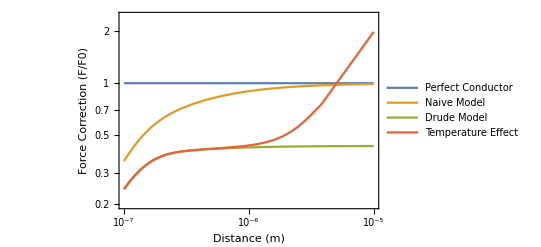

```mathematica
LogLogPlot[{1,Fcorrected[1,L,radius,0]/Fperfect[L,radius],Fcorrected[2,L,radius,0]/Fperfect[L,radius],Fcorrected[2,L,radius,300]/Fperfect[L,radius]},{L,1.0*^-7,1*^-5},Frame->True,PlotRangePadding->{None,0.1},PlotRange->{{1.*^-7,1*^-5},Full},FrameLabel->{"Distance (m)","Force Correction (F/F0)"},ImageSize->Scaled[0.8],PlotLegends->{"Perfect Conductor","Naive Model","Drude Model","Temperature Effect"}]
```

```mathematica
Fperfect[1*^-6,5*^6]
Table[Fperfect[L,0.113]*TempCorrection[300,L],{L,5*^-7,1*^-5,0.000001}]
```

0.0135558

{2.45989×10^-9,9.83092×10^-11,2.56736×10^-11,1.17428×10^-11,6.94528×10^-12,4.64933×10^-12,3.32881×10^-12,2.50031×10^-12,1.94661×10^-12,1.55837×10^-12}

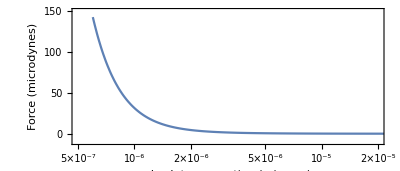

```mathematica
LogLinearPlot[Fperfect[L,0.113]*TempCorrection[300,L]/1*^-11,{L,6*^-7,10*^-5},PlotRange->{{0.5*^-6,20*^-6},{-10,150}},AspectRatio->3/7,Frame->True,FrameLabel->{"absolute separation (microns)","Force (microdynes)"},ImageSize->Scaled[0.8]]
```

```mathematica
data=Table[{10.0^(-7+x),Fperfect[10.0^(-7+x),sR],Fcorrected[1,10.0^(-7+x),sR,0],Fcorrected[2,10.0^(-7+x),sR,0],Fcorrected[2,10.0^(-7+x),sR,300]},{x,0,3,0.01}];
data2=Table[{10.0^(-7+x),FPFA[10.0^(-7+x),sR],FPFAcorrected[1,10.0^(-7+x),sR,0],FPFAcorrected[2,10.0^(-7+x),sR,0],FPFAcorrected[2,10.0^(-7+x),sR,300]},{x,0,3,0.01}];
```

```mathematica
Export[NotebookDirectory[]<>"calculated_vals.tsv",data];
Export[NotebookDirectory[]<>"calculated_pfa_vals.tsv",data2];
```

```mathematica
2*Pi*c/ωp[1]*10^6
```

0.137492